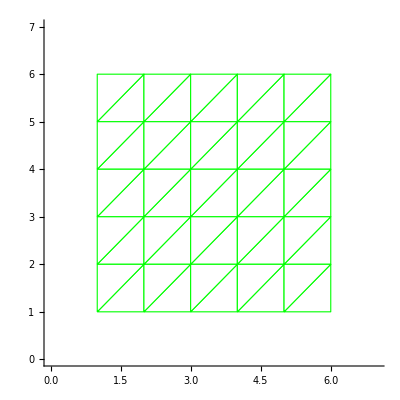

```mathematica
SetDirectory[NotebookDirectory[]];
uzel=Import["fileUzel.dat"];
triangle=Import["fileTriangle.dat"];
boundary=Import["fileBoundary.dat"];
Nu=Length[uzel];
Nt=Length[triangle];
Nb=Length[boundary];
Show[Graphics[{EdgeForm[Directive[Green]],White,Table[Polygon[{uzel[[triangle[[i]][[1]]]],uzel[[triangle[[i]][[2]]]],uzel[[triangle[[i]][[3]]]]}],{i,1,Nt}]},Axes->True,PlotRange->{{0,7},{0,7}},AspectRatio->Automatic],Graphics[{EdgeForm[Directive[Red]],White,Table[Polygon[{uzel[[triangle[[boundary[[i]][[1]]]][[boundary[[i]][[2]]]]]],uzel[[triangle[[boundary[[i]][[1]]]][[Mod[boundary[[i]][[2]],3]+1]]]]}],{i,1,Nb}]},Axes->True,PlotRange->{{0,7},{0,7}},AspectRatio->Automatic]]
```